# Introducción a los Modelos Matemáticos en Gestión Financiera — Proyecto 1

Nicolas Maldonado Baracaldo — 201423809

Universidad de Los Andes
Facultad de Ciencias
Departamento de Matemáticas

## Obtención de Datos para los Activos Escogidos

```mathematica
vEC=Flatten[Table[FinancialData["NYSE:EC","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rEC=Table[(vEC[[i]]-vEC[[i-1]])/vEC[[i-1]],{i,2,24}];
tsEC=TimeSeries[vEC,Automatic]
```

TimeSeries[…]

```mathematica
vAVH=Flatten[Table[FinancialData["NYSE:AVH","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rAVH=Table[(vAVH[[i]]-vAVH[[i-1]])/vAVH[[i-1]],{i,2,24}];
tsAVH=TimeSeries[vAVH,Automatic]
```

TimeSeries[…]

```mathematica
vCIB=Flatten[Table[FinancialData["NYSE:CIB","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rCIB=Table[(vCIB[[i]]-vCIB[[i-1]])/vCIB[[i-1]],{i,2,24}];
tsCIB=TimeSeries[vCIB,Automatic]
```

TimeSeries[…]

```mathematica
vTGLS=Flatten[Table[FinancialData["NASDAQ:TGLS","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rTGLS=Table[(vTGLS[[i]]-vTGLS[[i-1]])/vTGLS[[i-1]],{i,2,24}];
tsTGLS=TimeSeries[vTGLS,Automatic]
```

TimeSeries[…]

```mathematica
vAVAL=Flatten[Table[FinancialData["NYSE:AVAL","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rAVAL=Table[(vAVAL[[i]]-vAVAL[[i-1]])/vAVAL[[i-1]],{i,2,24}];
tsAVAL=TimeSeries[vAVAL,Automatic]
```

TimeSeries[…]

```mathematica
vBTI=Flatten[Table[FinancialData["NYSE:BTI","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rBTI=Table[(vBTI[[i]]-vBTI[[i-1]])/vBTI[[i-1]],{i,2,24}];
tsBTI=TimeSeries[vBTI,Automatic]
```

TimeSeries[…]

```mathematica
vAAPL=Flatten[Table[FinancialData["NASDAQ:AAPL","Open",{{i,j,1}}],{i,2018,2019},{j,1,12}]];
rAAPL=Table[(vAAPL[[i]]-vAAPL[[i-1]])/vAAPL[[i-1]],{i,2,24}];
tsAAPL=TimeSeries[vAAPL,Automatic]
```

TimeSeries[…]

### Visualización de las Series Temporales

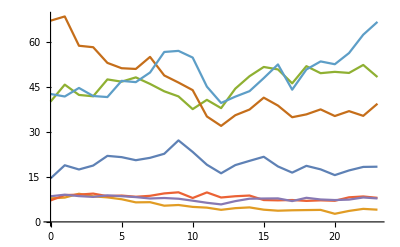

```mathematica
ListLinePlot[{tsEC,tsAVH,tsCIB,tsTGLS,tsAVAL,tsBTI,tsAAPL}]
```

## Cálculo de los Objetos Matemáticos

### Vectores û y r̄

```mathematica
û=Table[1,7]
r̄=Mean[Transpose[{rEC,rAVH,rCIB,rTGLS,rAVAL,rBTI,rAAPL}]];
NumberForm[%,{4,4}]
```

{1,1,1,1,1,1,1}

{0.0182,-0.0183,0.0112,0.0108,-0.0008,-0.0193,0.0237}

### Matriz de Covarianzas S

```mathematica
S=24/23 Covariance[Transpose[{rEC,rAVH,rCIB,rTGLS,rAVAL,rBTI,rAAPL}]];
NumberForm[%//MatrixForm,{3,3}]
```

(0.018 | 0.007 | 0.006 | 0.005 | 0.008 | 0.005 | 0.005
0.007 | 0.021 | 0.002 | 0.007 | 0.004 | 0.002 | 0.003
0.006 | 0.002 | 0.007 | 0.003 | 0.005 | 0.002 | 0.001
0.005 | 0.007 | 0.003 | 0.013 | 0.001 | -0.001 | -0.001
0.008 | 0.004 | 0.005 | 0.001 | 0.007 | 0.003 | 0.004
0.005 | 0.002 | 0.002 | -0.001 | 0.003 | 0.007 | 0.004
0.005 | 0.003 | 0.001 | -0.001 | 0.004 | 0.004 | 0.009)

#### Verificación de Propiedades de S

```mathematica
PositiveSemidefiniteMatrixQ[S]
Det[S]≠0
```

True

True

## Cálculo de Parámetros de la Teoría de la Cartera 𝒜, ℬ, 𝒞, 𝒟

```mathematica
𝒜=û.Inverse[S].û
ℬ=û.Inverse[S].r̄;
NumberForm[%,{4,4}]
𝒞=r̄.Inverse[S].r̄;
NumberForm[%,{4,4}]
𝒟=𝒜 𝒞-ℬ^2
```

381.14

1.4140

0.5482

206.955

## Cálculo de los Portafolios Óptimos

```mathematica
SuperStar[x][μ_]:=SuperStar[x][μ]=(𝒞-ℬ μ)/𝒟 Inverse[S].û+(𝒜 μ-ℬ)/𝒟 Inverse[S].r̄
```

```mathematica
SuperStar[x][0.5]
```

{3.087,-0.1877,10.2509,-1.15606,-14.125,-5.87528,9.0062}

```mathematica
SeedRandom[2248];
μ4=RandomVariate[UniformDistribution[{0,0.25}],4]
Table[SuperStar[x][μ4[[i]]],{i,1,4}]//MatrixForm
```

{0.0447933,0.124908,0.0286138,0.14924}

(0.0586242 | 0.00463106 | 1.25181 | 0.119285 | -1.27062 | -0.179155 | 1.01542
0.59161 | -0.0292187 | 2.83562 | -0.105173 | -3.53296 | -1.18166 | 2.42178
-0.0490139 | 0.0114671 | 0.931953 | 0.164614 | -0.81373 | 0.0233036 | 0.731406
0.75348 | -0.039499 | 3.31662 | -0.173342 | -4.22004 | -1.48612 | 2.84889)

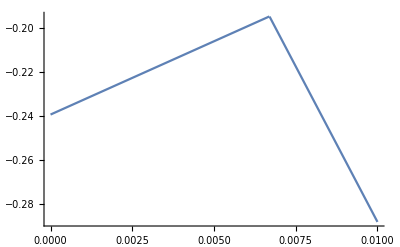

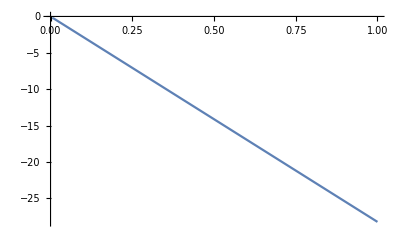

```mathematica
Plot[Min[SuperStar[x][μ]],{μ,0,0.01}]
Plot[Min[SuperStar[x][μ]],{μ,0,1}]
```

## Frontera Eficiente del Portafolio Escogido

```mathematica
Subscript[r, x][μ_]:=Subscript[r, x][μ]=SuperStar[x][μ].r̄
Subscript[σ, x][μ_]:=Subscript[σ, x][μ]=SuperStar[x][μ].S.SuperStar[x][μ]
```

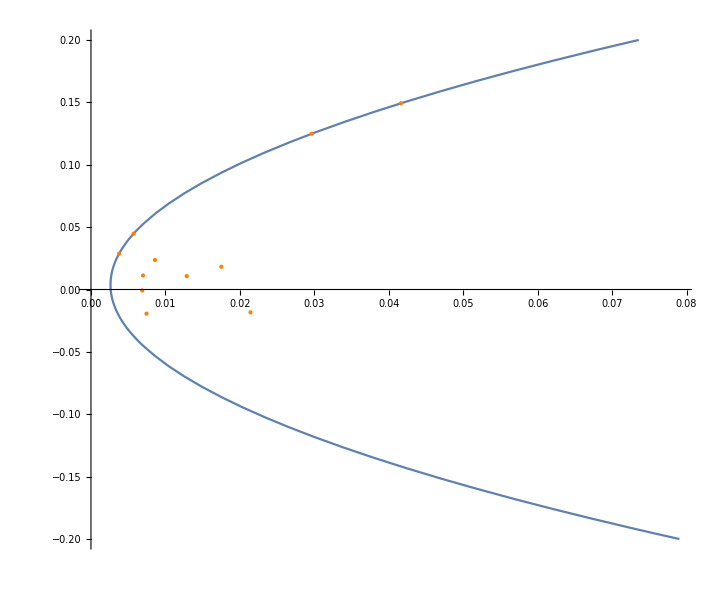

```mathematica
f=ParametricPlot[{Subscript[σ, x][μ],Subscript[r, x][μ]},{μ,-0.2,0.2}];
s=Graphics[{PointSize[Large],Orange,Point[Transpose[{Diagonal[S],r̄}]]}];
r4=Graphics[{PointSize[Large],Orange,Point[Table[{Subscript[σ, x][μ4[[i]]],Subscript[r, x][μ4[[i]]]},{i,1,4}]]}];
Show[{f,s,r4},ImageSize->{720,600},AspectRatio->Full]
```

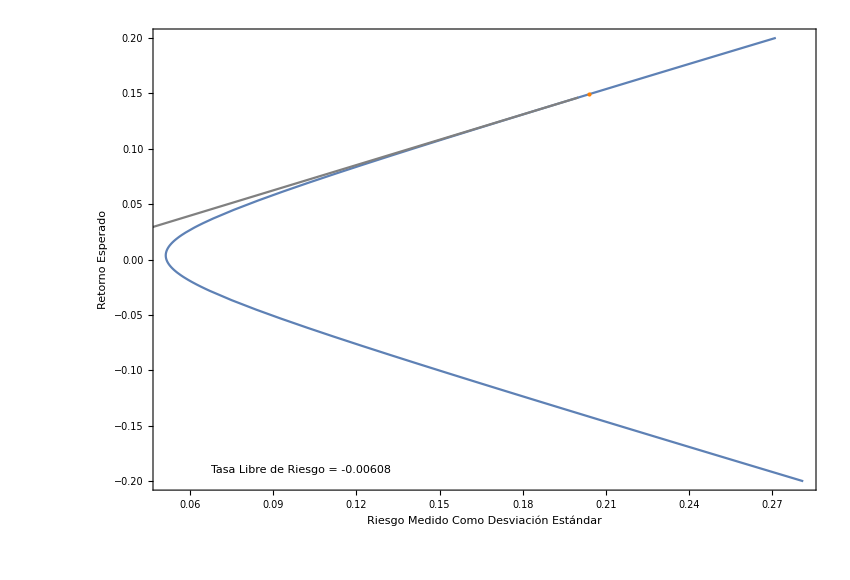

```mathematica
fsd=ParametricPlot[{√(Subscript[σ, x][μ]),Subscript[r, x][μ]},{μ,-0.2,0.2}];
r4sd=Table[Graphics[{PointSize[Large],Orange,Point[{√(Subscript[σ, x][μ4[[i]]]),Subscript[r, x][μ4[[i]]]}]}],{i,1,4}];
tl4=Table[Plot[(D[Subscript[r, x][μ], μ]/D[√(Subscript[σ, x][μ]), μ]/.{μ->μ4[[i]]})(sd-√(Subscript[σ, x][μ4[[i]]]))+Subscript[r, x][μ4[[i]]],{sd,0,0.20},PlotStyle->Gray],{i,1,4}];
rfr=Table[ToString[NumberForm[(D[Subscript[r, x][μ], μ]/D[√(Subscript[σ, x][μ]), μ]/.{μ->μ4[[i]]})(sd-√(Subscript[σ, x][μ4[[i]]]))+Subscript[r, x][μ4[[i]]]/.{sd->0},3]],{i,1,4}];
Show[{fsd,r4sd[[4]],tl4[[4]]},Frame->True,Axes->False,FrameLabel->{"Riesgo Medido Como Desviación Estándar","Retorno Esperado"},LabelStyle->"Subsubtitle",ImageSize->{850,580},AspectRatio->Full,Epilog->Inset[Framed[Style["Tasa Libre de Riesgo = "<>rfr[[4]],24]],{0.1,-0.19}]]
```

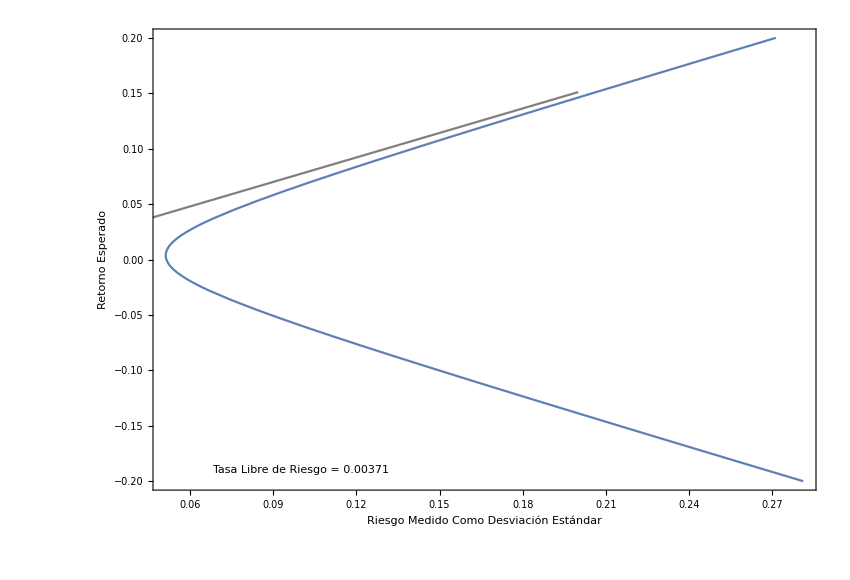

```mathematica
cml=Plot[(lim_(μ->∞) D[Subscript[r, x][μ], μ]/D[√(Subscript[σ, x][μ]), μ])(sd-√(Subscript[σ, x][2.5241947317990623*^6]))+Subscript[r, x][2.5241947317990623*^6],{sd,0,0.20},PlotStyle->Gray];
rfcm=ToString[NumberForm[(lim_(μ->∞) D[Subscript[r, x][μ], μ]/D[√(Subscript[σ, x][μ]), μ])(sd-√(Subscript[σ, x][2.5241947317990623*^6]))+Subscript[r, x][2.5241947317990623*^6]/.{sd->0},3]];
Show[{fsd,cml},Frame->True,Axes->False,FrameLabel->{"Riesgo Medido Como Desviación Estándar","Retorno Esperado"},LabelStyle->"Subsubtitle",ImageSize->{850,580},AspectRatio->Full,Epilog->Inset[Framed[Style["Tasa Libre de Riesgo = "<>rfcm,24]],{0.1,-0.19}]]
```

```mathematica
{Subscript[μ, min]}=Solve[D[√(Subscript[σ, x][μ]), μ]/D[Subscript[r, x][μ], μ]==0,μ];
SuperStar[x][μ]/. Subscript[μ, min]
√(Subscript[σ, x][μ])/. Subscript[μ, min]
Subscript[r, x][μ]/. Subscript[μ, min]
```

{-0.2147,0.0219898,0.439605,0.23439,-0.110452,0.334945,0.294221}

0.0512221

0.00370892

```mathematica
ret4=Table[Subscript[r, x][μ4[[i]]],{i,1,4}];
var4=Table[Subscript[σ, x][μ4[[i]]],{i,1,4}];
std4=Table[√(Subscript[σ, x][μ4[[i]]]),{i,1,4}];
rfr4=Table[(D[Subscript[r, x][μ], μ]/D[√(Subscript[σ, x][μ]), μ]/.{μ->μ4[[i]]})(sd-√(Subscript[σ, x][μ4[[i]]]))+Subscript[r, x][μ4[[i]]]/.{sd->0},{i,1,4}];
Grid[{{"","Portafolio 1","Portafolio 2","Portafolio 3","Portafolio 4"},Flatten[{{"Retorno Esperado"},ret4}],Flatten[{{"Varianza"},var4}],Flatten[{{"Desviación Estándar"},std4}],Flatten[{{"Tasa Libre de Riesgo"},rfr4}]}]
```

| Portafolio 1 | Portafolio 2 | Portafolio 3 | Portafolio 4
Retorno Esperado | 0.0447933 | 0.124908 | 0.0286138 | 0.14924
Varianza | 0.00573228 | 0.0296764 | 0.00376599 | 0.0416285
Desviación Estándar | 0.0757118 | 0.172268 | 0.0613677 | 0.204031
Tasa Libre de Riesgo | -0.0309672 | -0.00804563 | -0.0534946 | -0.00608039

```mathematica
Subscript[σ, M][μ_]:=(𝒜 μ^2-2μ ℬ+𝒞)/𝒟
Subscript[x, M][τ_]:=1/Total[(r̄-τ û).Inverse[S]](r̄-τ û).Inverse[S]
```

```mathematica
Table[μ4[[i]],{i,1,4}]
Table[Subscript[σ, M][μ4[[i]]],{i,1,4}]
```

{0.0447933,0.124908,0.0286138,0.14924}

{0.00573228,0.0296764,0.00376599,0.0416285}

```mathematica
Table[Subscript[x, M][rfr4[[i]]].r̄,{i,1,4}]
Table[Subscript[x, M][rfr4[[i]]].S.Subscript[x, M][rfr4[[i]]],{i,1,4}]
```

{0.0447933,0.124908,0.0286138,0.14924}

{0.00573228,0.0296764,0.00376599,0.0416285}

```mathematica
Solve[(r-τ)/(b-τ a)==σ,τ]
```

{{τ→(-r+b σ)/(-1+a σ)}}

```mathematica
τ[r_,σ_]:=(ℬ σ-r)/(𝒜 σ-1)
```

```mathematica
Table[τ[ret4[[i]],var4[[i]]],{i,1,4}]
```

{-0.0309672,-0.00804563,-0.0534946,-0.00608039}

```mathematica
SuperStar[x][μ4[[2]]]
```

{0.59161,-0.0292187,2.83562,-0.105173,-3.53296,-1.18166,2.42178}

```mathematica
β[μ_]:=(SuperStar[x][μ].S.SuperStar[x][μ4[[2]]])/(SuperStar[x][μ4[[2]]].S.SuperStar[x][μ4[[2]]])
```

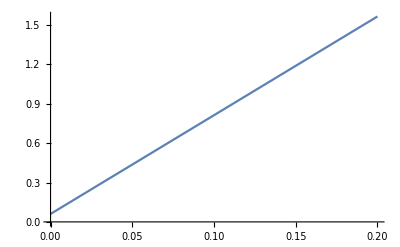

```mathematica
Plot[β1[μ],{μ,0,0.2}]
```